```mathematica
SetDirectory[NotebookDirectory[]];
Get["StockEntropy.m"];
```

Library for stock price entropy loaded (Jeremy Clark, 2010, BSD License).

## Graphs for a Stock

### Calulate

```mathematica
ticker="MSFT";

trials=100000;

prices1=FinancialData[ticker,"Close",DatePlus[{-1,"Year"}]];
prices=Part[prices1,All,2];

loghist=Slide[(Log[#2/#1])&,prices,2];
σimp=StandardDeviation[loghist];
μimp=Mean[loghist]+(1/2)*(σimp)^2;
stock=Stock[Last[prices],μimp,σimp];

mcpath=MonteCarloPath[stock,1,1000,10];
St=MonteCarlo[stock,1,1000,trials];
```

$Aborted

### Graph

```mathematica
Print[ticker," observed from ",First[prices1]," to ",Last[prices1]];
DateListPlot[prices1,AxesLabel->{"Price","Date"},Filling->Bottom,DateTicksFormat->{"MonthShort","/","YearShort"},ImageSize->100]

Print["Logrelative returns for ",ticker];
Histogram[loghist,{0.01},PlotRange->All,AxesLabel->{"Log-Return","Bins"},ImageSize->400]

Print["Simulating stock ",stock];
ListLinePlot[mcpath,AxesLabel->{"Time Steps","Price"},ImageSize->400]

Print["Histogram for entropy calculation (bins not to scale)"]
Histogram[St,PlotRange->All,AxesLabel->{"Price","Bins"},ImageSize->400]
```

## Graphs for Sample Dates from Paper

```mathematica
ticker="MSFT";

trials=100000;

prices1=FinancialData[ticker,"Close",{{2009,3,24},{2010,3,23}}];
prices=Part[prices1,All,2];

loghist=Slide[(Log[#2/#1])&,prices,2];
σimp=StandardDeviation[loghist];
μimp=Mean[loghist]+(1/2)*(σimp)^2;
stock=Stock[Last[prices],μimp,σimp];

mcpath=MonteCarloPath[stock,1,1000,10];
St=MonteCarlo[stock,1,1,trials]; 

(* Step 4: find spread of observed prices *)
Bins=Length[DeleteDuplicates[St]];
BinSpread=IntegerPart[Max[St]*100-Min[St]*100+1];

(* Step 5: estimate entropy *)
Ent=Entropy[2,St]//N
Bias=(BinSpread)/(2*trials)//N
EntAdj=Ent+Bias
```

7.76404

0.002195

7.76623

MSFT observed from {{2009,3,24},17.48} to {{2010,3,23},29.75}

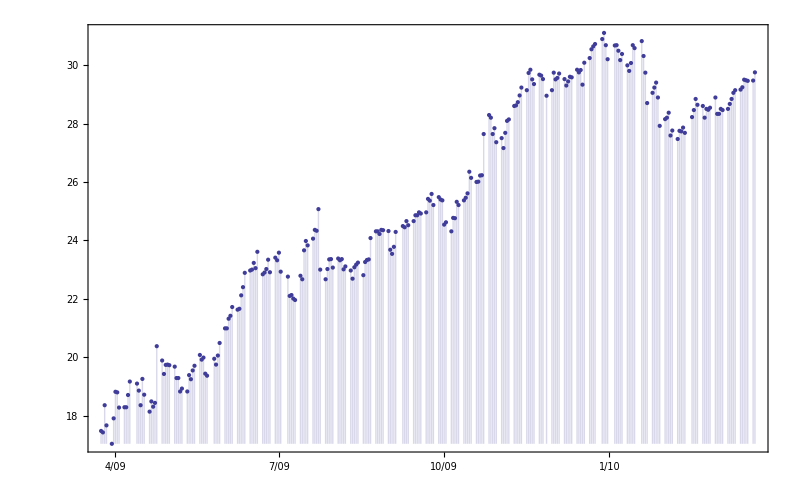

Logrelative returns for MSFT

-Graphics-

Simulating stock {29.75,0.00227429,0.0176455}

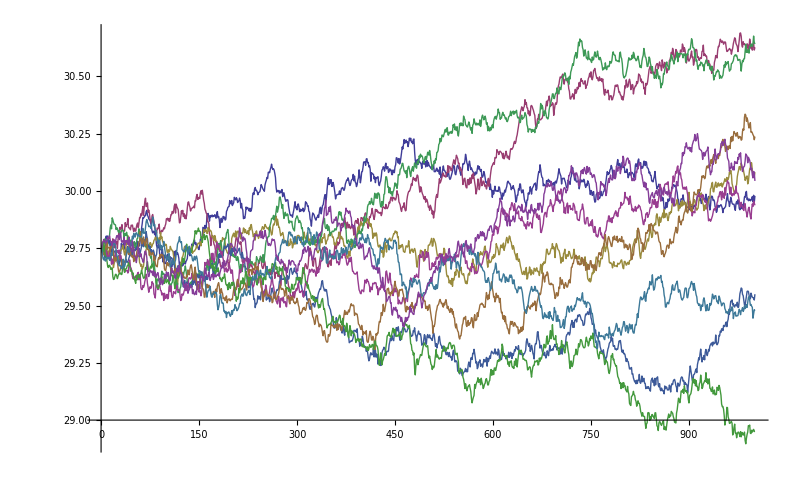

Histogram for entropy calculation (bins not to scale)

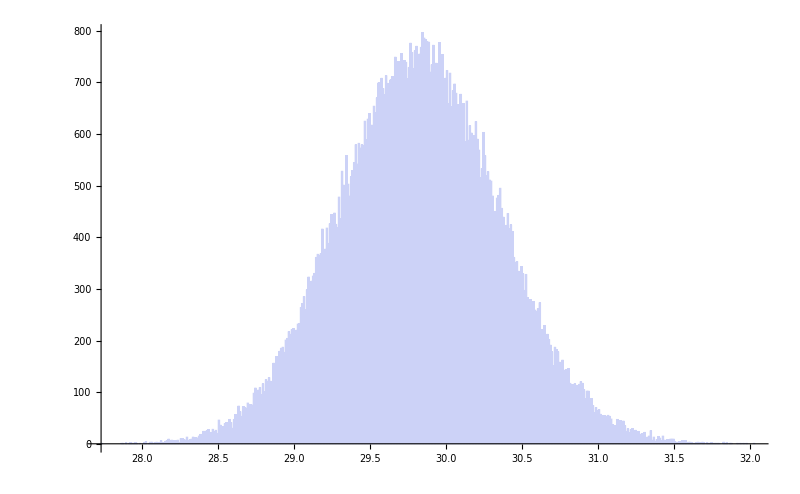

```mathematica
fs=40;

Print[ticker," observed from ",First[prices1]," to ",Last[prices1]];
DateListPlot[prices1,(*AxesLabel->{"Price","Date"},*) Filling->Bottom,DateTicksFormat->{"MonthShort","/","YearShort"},LabelStyle->{FontSize->fs},ImageSize->800]

Print["Logrelative returns for ",ticker];
Histogram[loghist,{0.001},PlotRange->All,(*AxesLabel->{"Log-Return","Bins"},*) LabelStyle->{FontSize->fs},ImageSize->800]

Print["Simulating stock ",stock];
ListLinePlot[mcpath,(*AxesLabel->{"Time Steps","Price"},*) LabelStyle->{FontSize->fs},ImageSize->800]

Print["Histogram for entropy calculation (bins not to scale)"]
Histogram[St,{0.01},PlotRange->All,(*AxesLabel->{"Price","Bins"},*) LabelStyle->{FontSize->fs},ImageSize->800,PerformanceGoal->"Speed"]
```